# Velociraptors

```mathematica
dist[t_,a_,vmax_]:= vmax^2 / a * Log[Cosh[a t / vmax]]
```

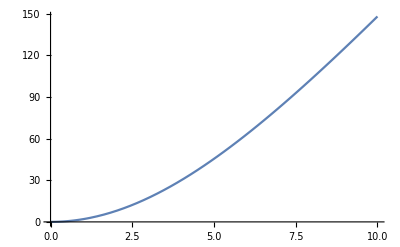

```mathematica
Plot[dist[t,4,25],{t,0,10}]
```

```mathematica
meetingpoints[t_,a1_,vmax1_,x1_, y1_,a2_,vmax2_,x2_,y2_]:={x,y}/.Solve[{dist[t,a1,vmax1]==Sqrt[(x-x1)^2+(y-y1)^2],dist[t,a2,vmax2]==Sqrt[(x-x2)^2+(y-y2)^2]},{x,y}]
```

```mathematica
ToPolar[lines_]:=SortBy[Table[{ArcTan[lines[[i,1]],lines[[i,2]]],Sqrt[lines[[i,1]]^2+lines[[i,2]]^2]},{i,1,Length[lines]}],First]
```

```mathematica
survdist[L_,ha_,hv_,aa_,av_,cripple_]:=
With[{p1x=0,p1y=L,p2x=-L*Sqrt[3]/2,p2y=-L/2,p3x=L*Sqrt[3]/2,p3y=-L/2},
With[{linterp1=Interpolation[ToPolar[Flatten[Cases[Normal[ ParametricPlot[meetingpoints[t,ha,hv,0,0,aa*cripple,av*cripple,p1x,p1y],{t,0,2*L},PlotRange->Full]],Line[i__]->i,Infinity],1]]],
linterp2=Interpolation[ToPolar[Flatten[Cases[Normal[ParametricPlot[meetingpoints[t,ha,hv,0,0,aa,av,p2x,p2y],{t,0,2*L},PlotRange->Full]],Line[i__]->i,Infinity],1]]],
linterp3=Interpolation[ToPolar[Flatten[Cases[Normal[ ParametricPlot[meetingpoints[t,ha,hv,0,0,aa,av,p3x,p3y],{t,0,2*L},PlotRange->Full]],Line[i__]->i,Infinity],1]]]},
With[{t=Table[Min[linterp1[x],linterp2[x],linterp3[x]],{x,-Pi,Pi,Pi/1000}]},
With[{r=Max[t],θ=N[(Position[t,Max[t]][[1,1]]-1)*2*Pi/(Length[t]-1)-Pi]},
If[Cos[θ]<0,{r Cos[Pi-θ],r Sin[θ]},{r Cos[θ],r Sin[θ]}]
]
]
]
]
```

```mathematica
PlotRingOfDeath[L_,ha_,hv_,aa_,av_,cripple_]:=With[{p1x=0,p1y=L,p2x=-L*Sqrt[3]/2,p2y=-L/2,p3x=L*Sqrt[3]/2,p3y=-L/2},With[{linterp1=Interpolation[ToPolar[Flatten[Cases[Normal[ ParametricPlot[meetingpoints[t,ha,hv,0,0,aa*cripple,av*cripple,p1x,p1y],{t,0,2*L},PlotRange->Full]],Line[i__]->i,Infinity],1]]],
linterp2=Interpolation[ToPolar[Flatten[Cases[Normal[ParametricPlot[meetingpoints[t,ha,hv,0,0,aa,av,p2x,p2y],{t,0,2*L},PlotRange->Full]],Line[i__]->i,Infinity],1]]],
linterp3=Interpolation[ToPolar[Flatten[Cases[Normal[ ParametricPlot[meetingpoints[t,ha,hv,0,0,aa,av,p3x,p3y],{t,0,2*L},PlotRange->Full]],Line[i__]->i,Infinity],1]]]},
With[{md=survdist[L,ha,hv,aa,av,cripple]},
Show[ParametricPlot[{meetingpoints[t,ha,hv,0,0,aa*cripple,av*cripple,p1x,p1y],meetingpoints[t,ha,hv,0,0,aa,av,p2x,p2y],meetingpoints[t,ha,hv,0,0,aa,av,p3x,p3y]},{t,0,L},PlotRange->{{-L,L},{-L,L}}],
ListPolarPlot[Table[N@{x,Min[linterp1[x],linterp2[x],linterp3[x]]},{x,-Pi,Pi,Pi/1000}],PlotStyle->{Red,Thickness[0.015]},Joined->True],
Graphics[{Black,Arrow[{{0,0},md}]}],
Graphics[{Blue,Disk[{p1x,p1y},L/33]}],
Graphics[{Orange,Disk[{p2x,p2y},L/33]}],
Graphics[{Green,Disk[{p3x,p3y},L/33]}],
Graphics[Text["Maximum distance: "<>ToString[Round[Sqrt[md[[1]]^2+md[[2]]^2],0.01]]<>"m\nDirection: "<>ToString[Round[(ArcTan[md[[1]],md[[2]]])*180/Pi,0.01]]<>" deg",{L/4,-3*L/4},{-0.75,0}]]
]
]
]
]
```

```mathematica
onevone[L_,ha_,hv_,aa_,av_]:={t,d}/.FindRoot[{dist[t,ha,hv]==d,dist[t,aa,av]==d+L},{{t,L},{d,L}}]
```

InterpolatingFunction::dmval: Input value {-π} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

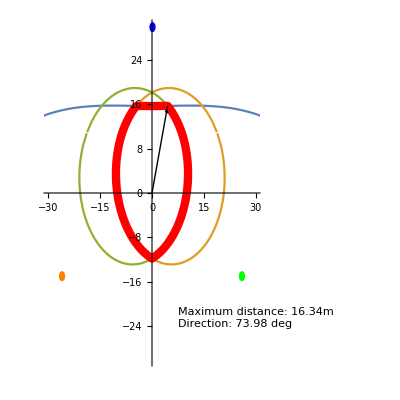

```mathematica
PlotRingOfDeath[30,2,7,4,25,0.4]
```

```mathematica
maxdist[Lmin_,Lmax_]:=With[{t=Table[survdist[L,2,7,4,25,0.4],{L,Lmin,Lmax}]},
{Range[Lmin,Lmax],Sqrt[t[[All,1]]^2+t[[All,2]]^2]}
]
```

InterpolatingFunction::dmval: Input value {-π} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Part::partw: Part 1 of {} does not exist.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

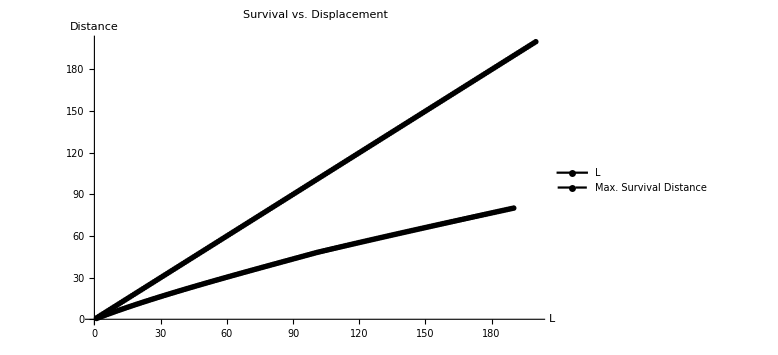

```mathematica
ListLinePlot[maxdist[1,200],PlotLabel->"Survival vs. Displacement",AxesLabel->{"L","Distance"},PlotLegends->{"L","Max. Survival Distance"},ImageSize->Large,PlotTheme->"Monochrome"]
```

```mathematica
improvementdirection[L_,baseha_,basehv_,da_,dv_]:=Module[{vp=onevone[L,baseha,basehv+dv,4,25][[2]],vm=onevone[L,baseha,basehv-dv,4,25][[2]],ap=onevone[L,baseha+da,basehv,4,25][[2]],am=onevone[L,baseha-da,basehv,4,25][[2]]},
{(ap-am)/(2*da),(vp-vm)/(2*dv)}
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

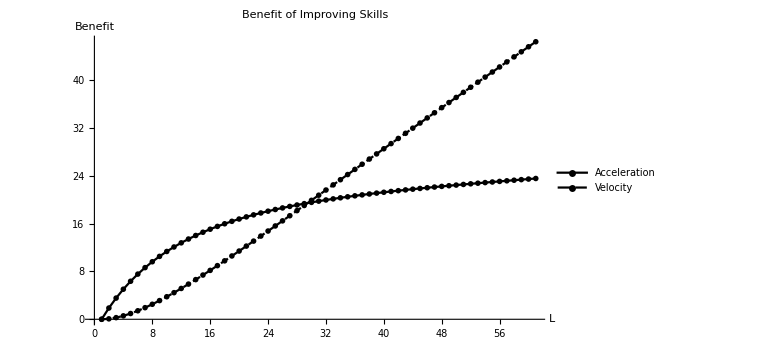

```mathematica
With[{id=Transpose[Table[improvementdirection[L,2,7,0.01*L+0.001,0.01*L+0.001],{L,0,60}]]},
ListLinePlot[{id[[1,All]]*(3-1),id[[2,All]]*(12-2)},PlotLabel->"Benefit of Improving Skills",AxesLabel->{"L","Benefit"},PlotLegends->{"Acceleration","Velocity"},ImageSize->Large,PlotTheme->"Monochrome"]
]
```